Física Matemática
Aula 2

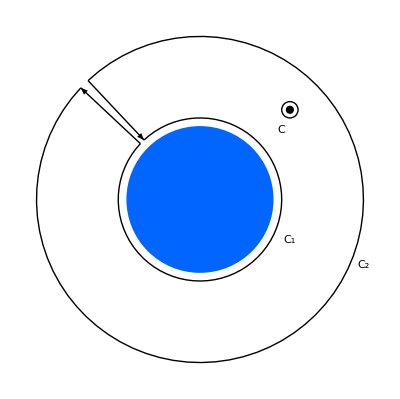

```mathematica
θ1=0.74π;θ2=-1.24π;pt1={Cos[θ1],Sin[θ1]};pt2={Cos[θ2],Sin[θ2]};Show[Graphics[{Circle[{0,0},1,{θ2,θ1}],Circle[{0,0},2,{-1.24π,0.74π}],Arrow[{2pt1,pt1}],Arrow[{pt2,2pt2}],{Hue[0.6],Disk[{0,0},0.9]},Circle[{1.1,1.1},0.1],Disk[{1.1,1.1},0.05],Text["C",{1,0.85}],Text["C_2",{2,-0.8}],Text["C_1",{1.1,-0.5}]}],AspectRatio->Automatic]
```

```mathematica
f[x_]:=Cos[x^2]
II[xx_] := Integrate[f[x],{x,0,xx}]
II[x]
II[∞]
```

√(π/2) FresnelC[√(2/π) x]

(√(π/2))/2

```mathematica
z[t_] := (1 + I)/(√2)t
Exp[I z[t]^2]D[z[t],t]
Integrate[%,t]
Integrate[%%,{t,-∞,0}]
```

((1+ⅈ) ⅇ^(-t^2))/(√2)

(1/2+ⅈ/2) √(π/2) Erf[t]

(1/2+ⅈ/2) √(π/2)